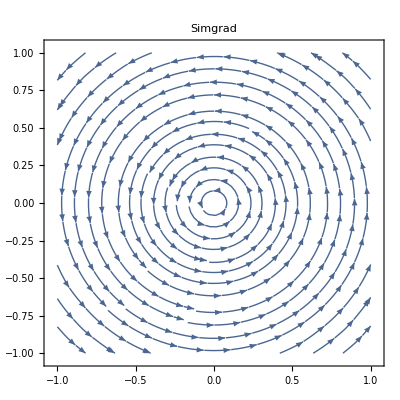

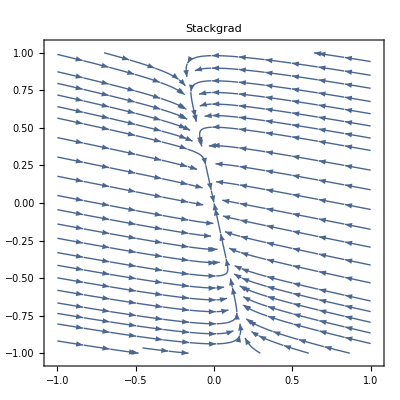

```mathematica
k1=0;
k2=.2;

f1=x1 x2 ;
f2=-x1 x2 ;
g1=D[f1,x1];
g2=D[f2,x2];
g1conj=D[f1,x1]-(D[D[f2,x1],x2]/(D[D[f2,x2],x2]+k2)) D[f1,x2];
StreamPlot[{-g1,-g2},{x1,-1,1},{x2,-1,1},PlotLabel->"Simgrad"]
StreamPlot[{-g1conj,-g2},{x1,-1,1},{x2,-1,1},PlotLabel->"Stackgrad"]
```